```mathematica
microrun[aDM_,MDVB_,MXd_,gSM_]:=(
$micropath="/home/isanderson/src/physics/micromegas_5.0.8/SMDP";
$microout="microout";
$paramsfile="paramsfile.par";
SetDirectory[$micropath];
params={{"aDM",aDM},{"MDVB",MDVB},{"MXd",MXd},{"gSM",gSM}};
Export[$paramsfile,params,"Table"];
Run["./main "<>$paramsfile<>" > "<>$microout];
str=OpenRead[$microout];
capline = Find[str,"Capture Rate is"];
capstring=StringTake[capline,-13];
capstring=StringReplace[capstring,"E+"-> "*10^"];
capstring=StringReplace[capstring,"E-"-> "*10^-"];
caprate=ToExpression[capstring];

crosspbline=Find[str,"proton  SI"];
crosspbstring=StringTake[crosspbline,{13,21}];
crosspbstring=StringReplace[crosspbstring,"E+"-> "*10^"];
crosspbstring=StringReplace[crosspbstring,"E-"-> "*10^-"];
crosspb=ToExpression[crosspbstring];
crossm2=crosspb*10^-36(*pb to cm^2*)*10^-4(*cm^2 to m^2*);
Close[str];
SetDirectory[NotebookDirectory[]];
{crossm2,caprate})
inMXd=100000.;
inaDM=0.024/1000 inMXd;
inMDVB=0.05;
ingSM=10^-8.;
microrun[inaDM,inMDVB,inMXd,ingSM]
```

{5.181×10^-43,5.10516×10^20}

Annihilation Rate From Sun

## Import Solar Data and constants

```mathematica
SetDirectory[NotebookDirectory[]];

build=0;(*build will have to be set to 1 if first time running, to generate interpolation tables*)

k=2.5; (*See 1602.01465 Eq. 15/16 for what these constants are*)
u0 = 245 10^3; 
uS=233 10^3;
vgal = 550 10^3;(*Galactic escape velocity*)
SR=6.957 10^8;(*Solar radius*)
ρχ=0.3 10^6(*Local dark matter density; PDG says 0.3 GeV/c^2 per cm^-3 = 10^6*0.3 GeV/c^2 per m^-3 *);
Gconst=6.67408 10^-11;
mp=0.938272(*proton mass, GeV*);
SSM=Import["data/SSM.dat"];
(*The lighter elements seem to have density as a function of radius, so I pulled these functions from *)
(*NB These appear to be mass fractions, not fraction by number. If the second entry is divided by the mass number then it will be fraction by number.*)
Hab=Table[{SSM[[i,2]]*SR,SSM[[i,7]]},{i,2,Length[SSM]}];
He4ab=Table[{SSM[[i,2]]*SR,SSM[[i,8]](*/4*)},{i,2,Length[SSM]}];
He3ab=Table[{SSM[[i,2]]*SR,SSM[[i,9]](*/3*)},{i,2,Length[SSM]}];
C12ab=Table[{SSM[[i,2]]*SR,SSM[[i,10]](*/12*)},{i,2,Length[SSM]}];
N14ab=Table[{SSM[[i,2]]*SR,SSM[[i,11]](*/14*)},{i,2,Length[SSM]}];
O16ab=Table[{SSM[[i,2]]*SR,SSM[[i,12]](*/16*)},{i,2,Length[SSM]}];
Habf=Interpolation[Hab,InterpolationOrder->1];
He4abf=Interpolation[He4ab];
He3abf=Interpolation[He3ab];
C12abf=Interpolation[C12ab];
N14abf=Interpolation[N14ab];
O16abf=Interpolation[O16ab];

(*Solar mass density importing data*)
(*SMD=Import["data/SolarMassDensity.csv"](*//ToExpression*)(*r/R_⊙, kg/m^3*);
SMDtab=Table[{SMD[[i,1]]*SR,SMD[[i,2]]},{i,1,Length[SMD]}];
SMDi=Interpolation[SMDtab,InterpolationOrder->1];*)

SMD=Table[{SSM⟦i,2⟧*SR,SSM⟦i,4⟧*0.001(*kg/g*)100^3(*cm^3/m^3*)},{i,2,Length[SSM]}];
SMDi=Interpolation[SMD,InterpolationOrder->1];

SM=1.989 10^30;
(*NIntegrate[SMDi[x]4π x^2,{x,0,SR}]*)
(*Htnf is the total fraction by number of hydrogen in the sun*)
Htnf=0.912;
(*Htmf is the total fraction by mass of hydrogen in the sun*)
Htmf=0.710;
(*Total number of atoms in the sun*)
tn=(Htmf*SM)/(1.007825 au Htnf)/.{au->1.660539 10^-27(*kg*)}
tnd=tn/(4/3 π SR^3)(*Atoms per m^3*);

(*The function tnf takes the astrophysical parameter logϵX for a particular element in the sun and outputs the total number fraction of the sun (e.g. what fraction of the sun is that element by number). The values are taken from 1405.0279 and 1405.0287*)
tnf[logϵX_]:=10^logϵX/10^12;
logϵ={(*H*)12.00,(*He*)10.93,(*C*)8.39,(*N*)7.78,(*O*)8.66,(*Ne*)7.84,(*Mg*)7.53,(*Si*)7.51,(*S*)7.14,(*Fe*)7.45,(*Na*)6.17,(*Al*)6.37,(*Cl*)5.50,(*Ar*)6.18,(*Ca*)6.31,(*Cr*)5.64,(*Ni*)6.23};(*ORIGINAL: {(*Mg*) 7.59, (*Si*) 7.51, (*P*) 5.41, (*S*) 7.12, (*K*) 5.04, (*Ca*) 6.32, (*Sc*) 3.16, (*Ti*) 4.93, (*V*) 3.89, (*Cr*) 5.62, (*Mn*) 5.42, (*Fe*) 7.47, (*Co*) 4.93, (*Ni*) 6.20};*)


(*Table of constant number densities for heavier atoms, number/m^3*)
ndtab=tnd Table[tnf[logϵ⟦i⟧],{i,1,Length[logϵ]}];


(*These are number densities of atoms, number/m^3, radius dependent*)
Hnd[x_]:=SMDi[x]Habf[x]/Hmass/.{Hmass-> 1.007825 au}/.{au->1.660539 10^-27(*kg*)}
He4nd[x_]:=SMDi[x]He4abf[x]/Hmass/.{Hmass-> 4.002602 au}/.{au->1.660539 10^-27(*kg*)}
He3nd[x_]:=SMDi[x]He3abf[x]/Hmass/.{Hmass-> 3.0160293 au}/.{au->1.660539 10^-27(*kg*)}
C12nd[x_]:=SMDi[x]C12abf[x]/Hmass/.{Hmass-> 12 au}/.{au->1.660539 10^-27(*kg*)}
N14nd[x_]:=SMDi[x]N14abf[x]/Hmass/.{Hmass-> 14.003074 au}/.{au->1.660539 10^-27(*kg*)}
O16nd[x_]:=SMDi[x]O16abf[x]/Hmass/.{Hmass-> 15.994915 au}/.{au->1.660539 10^-27(*kg*)}

(*Table of number densities assuming same distribution as Oxygen*)
ndftab[x_]:=tnf[Drop[logϵ,5]]/tnf[8.66] Hold[O16nd[x]]
nd[y_,i_]:=Join[{Hold[Hnd[x]],Hold[He4nd[x]],Hold[C12nd[x]],Hold[N14nd[x]],Hold[O16nd[x]]},ndftab[x]]⟦i⟧/.{x-> y}//ReleaseHold;
ndplottab[y_]:=Join[{Hold[Hnd[x]],Hold[He4nd[x]],Hold[C12nd[x]],Hold[N14nd[x]],Hold[O16nd[x]]},ndftab[x]]/.{x-> y}//ReleaseHold;
(*ORIGINAL: nd[y_,i_]:=Join[{Hold[Hnd[x]],Hold[He4nd[x]],Hold[He3nd[x]],Hold[C12nd[x]],Hold[N14nd[x]],Hold[O16nd[x]]},ndtab]⟦i⟧/.{x-> y}//ReleaseHold;*)
(*These lists are for:
MICROMEGAS: {1 H, 2 He4, 3 C12, 4 N14, 5 O16, 6 Ne20, 7 Mg24, 8 Si28, 9 S32, 10 Fe56, 11 Na23, 12 Al27, 13 Cl35, 14 Ar40, 15 Ca40, 16 Cr52, 17 Ni59}
ORIGINAL: {1 H1, 2 He4, 3 He3, 4 C12, 5 N14, 6 O16, 7 Mg, 8 Si, 9 P, 10 S, 11 K, 12 Ca, 13 Sc, 14 Ti, 15 V, 16 Cr, 17 Mn, 18 Fe, 19 Co, 20 Ni}*)
ZN:={1,2,6,7,8,10,12,14,16,26,11,13,17,18,20,24,28};(*ORIGINAL: {1,2,2,6,7,8,12,14,15,16,19,20,21,22,23,24,25,26,27,28};*)

mN:={1.007825 ,4.002602,12,14.003074,15.994915,19.99,23.985,27.977,31.972,55.85,22.9877,26.98153,34.969,39.962,39.963,51.941,58.934}au/.{au-> 0.9314941 (*GeV*)};
(*ORIGINAL: {1.007825 ,4.002602,3.0160293,12,14.003074,15.994915,24.305, 28.085,30.974,32.06,39.098,40.078,44.956,47.867,50.942,51.996,54.938,55.845,58.933,58.693}au/.{au-> 0.9314941 (*GeV*)};*)

AN:={1,4,12,14,16,20,24,28,32,56,23,27,35,40,40,52,59};
(*ORIGINAL: {1,4,3,12,14,16,24,28,31,32,39,40,45,48,51,52,55,56,59,59};*)
```

9.25261×10^56

```mathematica
(1.989 10^30 kg)/(1.007825 au)/.{au->1.660539 10^-27 kg}
```

1.1885×10^57

## Generating Functions

### Generate Escape Velocity

```mathematica
If[build==1,
Mtab=Table[{r,NIntegrate[SMDi[rp]4π rp^2,{rp,0,r}]},{r,0,SR,SR/100.}];
Mi=Interpolation[Mtab,InterpolationOrder->1];
Export["data/Mass.csv",Mtab,"CSV"];
vetab= Table[{r,√(-2(NIntegrate[(Gconst Mi[rp])/rp^2,{rp,SR,r}]-(Gconst Mi[SR])/SR))},{r,SR/100,SR,SR/100}];
vetab=Prepend[vetab,{0.0001,√(-2(NIntegrate[(Gconst Mi[rp])/rp^2,{rp,SR,0.001}]-(Gconst Mi[SR])/SR))}];
Export["data/Escape.csv",vetab,"CSV"];]
```

### Generate fS

```mathematica
If[build==1,
fnonorm[u_]:=(*norm*) (Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
(*normconstant=1/NIntegrate[fnonorm[√(x^2+y^2+z^2)],{x,0,vgal},{y,0,vgal},{z,0,vgal}]*)
normconstant=1/NIntegrate[4π u^2 fnonorm[u],{u,0,vgal}];

f[u_]:=normconstant(Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
usolve=Solve[u^2+uS^2+2u uS c==vgal^2,u][[2]];
upint=u/.usolve/.{c->-1};
Export["data/upint.csv",upint,"CSV"];
fS[u_] := 1/2 NIntegrate[f[√(u^2+uS^2+2u uS c)],{c,-1,1}];
ftab=Table[{u,f[u]},{u,0.,upint,upint/1000}];
Export["data/f.csv",ftab,"CSV"];
fStab=Table[{u,fS[u]},{u,0.,upint,upint/1000}];
Export["data/fS.csv",fStab,"CSV"];]
```

### Generate Integrals

```mathematica
If[build==1,
fStab=Import["data/fS.csv"]//ToExpression;
fSi=Interpolation[fStab];
vetab=Import["data/Escape.csv"]//ToExpression;
vei=Interpolation[vetab,InterpolationOrder->1];
nint1=NIntegrate[4π u(u^2)fSi[u],{u,0,upint}];
Export["data/nint1.csv",nint1,"CSV"];
nint2=NIntegrate[4π u fSi[u],{u,0,upint}];
Export["data/nint2.csv",nint2,"CSV"];
wint[r_]:=nint1+vei[r]^2 nint2;
wrint=NIntegrate[4 π r^2 O16nd[r]wint[r],{r,0,SR}];
Export["data/wrint.csv",wrint,"CSV"];]
```

### Generate Ei

```mathematica
If[build==1,
Ea[z_]:=-NIntegrate[Exp[-t]/t,{t,-z,∞}];
Etab=Table[{-Exp[lnz],Ea[-Exp[lnz]]},{lnz,-10,10,0.1}];
Export["data/Ei.csv",Etab,"CSV"];]
```

## Actual Program

```mathematica
vetab=Import["data/Escape.csv"]//ToExpression;
vei=Interpolation[vetab,InterpolationOrder->1];
fStab=Import["data/fS.csv"]//ToExpression;
fSi=Interpolation[fStab];
ftab=Import["data/f.csv"]//ToExpression;
fi=Interpolation[ftab];
nint1=Import["data/nint1.csv"][[1,1]]//ToExpression;
nint2=Import["data/nint2.csv"][[1,1]]//ToExpression;
wrint=Import["data/wrint.csv"][[1,1]]//ToExpression;
upint=Import["data/upint.csv"][[1,1]]//ToExpression;
Etab=Import["data/Ei.csv"]//ToExpression;
Ei=Interpolation[Etab];
Mtab=Import["data/Mass.csv"]//ToExpression;
Mi=Interpolation[Mtab];
Emax[r_,u_,mχ_,mn_]:=(*1./GeV*)(*Desired units of GeV*)(2 μN^2(*GeV^2/c^4*)( u^2+vei[r]^2)(*m^2/s^2*))/(mn (*GeV/c^2*))1/c^2/.{μN-> (mχ mn)/(mχ+mn),c->3 10^8};

Emin[r_,u_,mχ_,mn_]:=(*1./GeV*)(*Desired units of GeV*)1/2 mχ (1(*GeV*))/c^2 u^2  (*m^2/s^2*)/.{c-> 3 10^8(*m/s*)};

(*This finds an upper limit on u based on the heaviside theta*)
(*Solve[Emax[SR,u,mχ,Nt]-Emin[SR,u,mχ,Nt]==0,u]*)
upintHS[mχ_,mNu_]:=((0.+8.439776214093713*^6 ) √mχ √mNu)/((mχ+mNu) √(9.-(36. mχ mNu)/(mχ+mNu)^2));

EN[An_]:=(*1/GeV*)(*Desired units of GeV*)0.114/An^(5/3) (*GeV*);

integrandr[r_,i_]:=4π r^2 nd[r,i];
integrandu[r_,u_]:=4π u(u^2+vei[r]^2)fSi[u];

Δmax[r_,u_,mχ_,mi_]:=(4 mi mχ)/(mχ + mi)^2;
Δmin[r_,u_,mχ_,mi_]:=u^2/(u^2+vei[r]^2);
Pri[r_,u_,mχ_,mi_]:=Max[0,(Δmax[r,u,mχ,mi]-Δmin[r,u,mχ,mi])/Δmax[r,u,mχ,mi]];
σi[mχ_,i_,σSI_,σSD_,mi_,A_,Z_]:=If[i==1,σSI+σSD,(mi^2 (mp+mχ)^2 Z^2 σSI)/(mp^2 (mi+mχ)^2)(*(A^2 σSI (mi/mp)^2(mp+mχ)^2)/(mi+mχ)^2*)(*+(A^2 σSD (mp+mχ)^2)/(mi+mχ)^2*)](*m^2*);

(*See 1702.02768 for this scaling*)
CNcap[mχ_,i_,σSI_,σSD_]:=nχ Block[ {mNt,ZNt,ANt,ENt},
mNt=mN[[i]];
ZNt=ZN[[i]];
ANt=AN[[i]];
ENt=EN[ANt];
σi[mχ,i,σSI,σSD,mNt,ANt,ZNt] NIntegrate[
integrandr[r,i]integrandu[r,u]Pri[r,u,mχ,mNt],
{r,0,SR},{u,0,(*upint*)upintHS[mχ,mNt]},WorkingPrecision->4,Method-> {Automatic,"SymbolicProcessing"->0}]]/.{nχ-> ρχ/mχ};

CTcap[mχ_,σSI_,σSD_]:=Sum[CNcap[mχ,i,σSI,σSD],{i,4,4(*Length[ZN]*)}];

Γann [mχ_,σSI_,σSD_]:= 1/2 CTcap[mχ,σSI,σSD](*Tanh[τS/τ[mχ,mA,ϵ,αχ]]^2*)
microsi[mχ_,i_]:=(μp0=(mχ mN⟦1⟧)/(mχ +mN⟦1⟧);
pA0=(4.4911577516764815*^15 √microσcap⟦1⟧)/(AN⟦1⟧ μp0);
4/π(ZN⟦i⟧pA0 (mχ mN⟦i⟧)/(mχ +mN⟦i⟧))^2 3.8937966 10^8 10^-40)
micropA0[mχ_]:=(μp0=(mχ mN⟦1⟧)/(mχ +mN⟦1⟧);
(4.4911577516764815*^15 √microσcap⟦1⟧)/(AN⟦1⟧ μp0))


(*Dark Photon Stuff*)
EDDmax[u_,mχ_,mn_]:=(*1./GeV*)(*Desired units of GeV*)(2 μN^2(*GeV^2/c^4*)( u^2)(*m^2/s^2*))/(mn (*GeV/c^2*))1/c^2/.{μN-> (mχ mn)/(mχ+mn),c->2.99792458 10^8};

fnonorm[u_]:=(*norm*) (Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
normconstant=1/NIntegrate[4π u^2 fnonorm[u],{u,0,vgal}];

f[u_]:=normconstant(Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
usolve=Solve[u^2+uS^2+2u uS c==vgal^2,u][[2]];
upint=u/.usolve/.{c->-1};
fS[u_] := 1/2 NIntegrate[f[√(u^2+uS^2+2u uS c)],{c,-1,1}];
ftab=Table[{u,f[u]},{u,0.,upint,upint/1000}];
fStab=Table[{u,fS[u]},{u,0.,upint,upint/1000}];
fSi=Interpolation[fStab];

vEesc=11186.;

integranduDD[u_]:=4π (u^2+vEesc^2)fSi[u];
dσDDdE[u_,mχ_,mA_,ϵ_,αχ_,ER_,mn_,Zn_,En_]:= 8 π ϵ^2 αχ α Zn^2 mn/((u^2+vEesc^2)(2mn ER +mA^2)^2)Exp[-ER/En] ℏ^2 c^4/.{α-> 1/137.}/.{ℏ-> 6.582119 10^-22 0.001 }/.{c-> 2.99792458 10^8 };
σDD[mχ_,mA_,ϵ_,αχ_,mN_,ZN_,EN_]:=NIntegrate[
dσDDdE[vgal,mχ,mA,ϵ,αχ,ER,mN,ZN,EN],
{ER,0,10(*EDDmax[u,mχ,mN]*)},WorkingPrecision->4,Method-> {Automatic,"SymbolicProcessing"->0}];

σDD[inMXd,inMDVB,ingSM,inaDM,mN⟦atomnumber⟧,ZN⟦atomnumber⟧,EN[AN⟦atomnumber⟧]]

σDDa[mχ_,mA_,ϵ_,αχ_,mn_,zn_]:=(4 μA^2)/π zn^2 fp^2 ℏ^2 c^2/.{μA-> (mχ mn)/(mχ+mn),fp-> (eχ e ϵ)/mA^2}/.{eχ-> √(4π αχ),e-> √(4π α)}/.{α-> 1/137.}/.{ℏ-> 6.582119 10^-22 0.001}/.{c-> 2.99792458 10^8 }
6.395*^-58
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

7.335×10^-52

6.395×10^-58

```mathematica
NIntegrate[
dσDDdE[vgal,inMXd,inMDVB,ingSM,inaDM,ER,mN⟦atomnumber⟧,ZN⟦atomnumber⟧,EN[AN⟦atomnumber⟧]],
{ER,0,10(*EDDmax[u,mχ,mN]*)},WorkingPrecision->4,Method-> {Automatic,"SymbolicProcessing"->0}]
```

2.23×10^-42

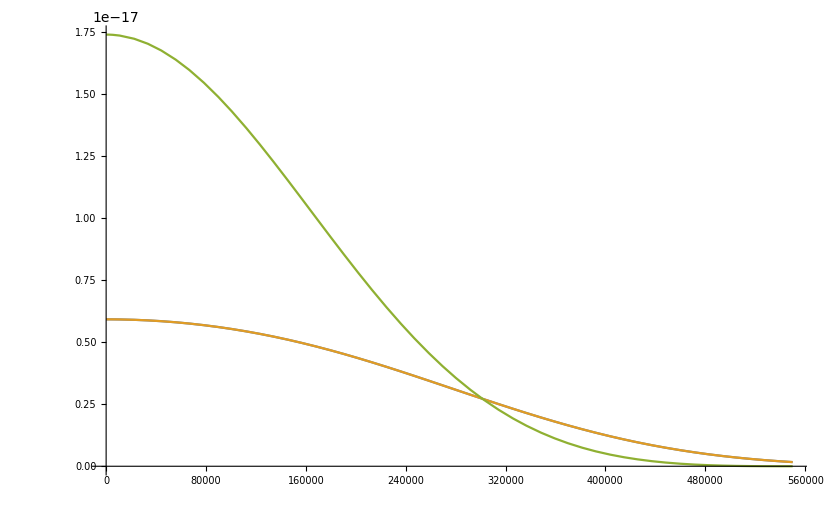

```mathematica
Plot[{fS[u],fSi[u],f[u]},{u,0,vgal}]
```

```mathematica
mn/((u^2)(2mn ER +mA^2)^2)Exp[-ER/En] ℏ^2 c^4/.{α-> 1/137.}/.{ℏ-> 6.582119 10^-22 0.001 GeV s}/.{c-> 2.99792458 10^8 m/s}/.{mn-> GeV,ER-> GeV,mA-> GeV,En-> GeV,u-> m/s}
```

(1.43047×10^-16 m^2)/GeV

```mathematica
runboth[MXd_,MDVB_,gSM_,aDM_]:=(
microσcap=microrun[aDM,MDVB,MXd,gSM];
analyticcap=CTcap[MXd,microσcap⟦1⟧,0.];
{aDM,MDVB,MXd,gSM,microσcap⟦1⟧,microσcap⟦2⟧,analyticcap})
inMXd=100000.;
inaDM=0.024/1000 inMXd;
inMDVB=0.05;
ingSM=10^-8.;
runboth[inMXd,inMDVB,ingSM,inaDM]
(%[[7]])/(%[[6]])
AN[[4]]

atomnumber=1;
σi[inMXd,atomnumber,microσcap⟦1⟧,0.,mN[[atomnumber]],AN[[atomnumber]],ZN[[atomnumber]]]
σDD[inMXd,inMDVB,ingSM,inaDM,mN⟦atomnumber⟧,ZN⟦atomnumber⟧,EN[AN⟦atomnumber⟧]]

(6.396*^-57)/(2.3875400620185935*^-56)
% σDDa[inMXd,inMDVB,ingSM,inaDM,mN⟦atomnumber⟧,ZN⟦atomnumber⟧]
1/(%%)
```

{2.4,0.05,100000.,1.×10^-8,5.181×10^-43,3.2694×10^19,5.01107×10^19}

1.53272

14

5.181×10^-43

9.715×10^-41

0.267891

5.18076×10^-43

3.73286

```mathematica
tab=Table[runboth[10^lMDVB,10.^4,10.^-8],{lMDVB,-2,2,0.1}];
```

```mathematica
plottab=Table[{tab⟦i,2⟧,tab⟦i,-1⟧/tab⟦i,-2⟧},{i,Length[tab]}];
ListLogLogPlot[plottab]
```

-Graphics-

```mathematica
(A^2 σSI (mi/mp)^2(mp+mχ)^2)/(mi+mχ)^2
(μAi/μp)^2 A^2 σSI/.{μAi-> (mi mχ)/(mi+mχ),μp-> (mp mχ)/(mp+mχ)}
(μAi/μp)^2 Zi^2 σSI/.{μAi-> (mi mχ)/(mi+mχ),μp-> (mpt mχ)/(mpt+mχ)}
```

(1.13591 A^2 mi^2 (0.938272+mχ)^2 σSI)/(mi+mχ)^2

(1.13591 A^2 mi^2 (0.938272+mχ)^2 σSI)/(mi+mχ)^2

(mi^2 (mpt+mχ)^2 Zi^2 σSI)/(mpt^2 (mi+mχ)^2)

```mathematica
Solve[si==4/π(Ai pA mu)^2 3.8937966 10^8 10^-40(*m^2*),pA]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{pA→-(4.49116×10^15 √si)/(Ai mu)},{pA→(4.49116×10^15 √si)/(Ai mu)}}

```mathematica
SetDirectory[NotebookDirectory[]];

build=0;(*build will have to be set to 1 if first time running, to generate interpolation tables*)

k=2.5; (*See 1602.01465 Eq. 15/16 for what these constants are*)
u0 = 245 10^3; 
uS=233 10^3;
vgal = 550 10^3;(*Galactic escape velocity*)
SR=6.957 10^8;(*Solar radius*)
ρχ=0.3 10^6(*Local dark matter density; PDG says 0.3 GeV/c^2 per cm^-3 = 10^6*0.3 GeV/c^2 per m^-3 *);
Gconst=6.67408 10^-11;
mp=0.938272(*proton mass, GeV*);
SSM=Import["data/SSM.dat"];
(*The lighter elements seem to have density as a function of radius, so I pulled these functions from *)
(*NB These appear to be mass fractions, not fraction by number. If the second entry is divided by the mass number then it will be fraction by number.*)
Hab=Table[{SSM[[i,2]]*SR,SSM[[i,7]]},{i,2,Length[SSM]}];
He4ab=Table[{SSM[[i,2]]*SR,SSM[[i,8]](*/4*)},{i,2,Length[SSM]}];
He3ab=Table[{SSM[[i,2]]*SR,SSM[[i,9]](*/3*)},{i,2,Length[SSM]}];
C12ab=Table[{SSM[[i,2]]*SR,SSM[[i,10]](*/12*)},{i,2,Length[SSM]}];
N14ab=Table[{SSM[[i,2]]*SR,SSM[[i,11]](*/14*)},{i,2,Length[SSM]}];
O16ab=Table[{SSM[[i,2]]*SR,SSM[[i,12]](*/16*)},{i,2,Length[SSM]}];
Habf=Interpolation[Hab,InterpolationOrder->1];
He4abf=Interpolation[He4ab];
He3abf=Interpolation[He3ab];
C12abf=Interpolation[C12ab];
N14abf=Interpolation[N14ab];
O16abf=Interpolation[O16ab];

(*Solar mass density importing data*)
(*SMD=Import["data/SolarMassDensity.csv"](*//ToExpression*)(*r/R_⊙, kg/m^3*);
SMDtab=Table[{SMD[[i,1]]*SR,SMD[[i,2]]},{i,1,Length[SMD]}];
SMDi=Interpolation[SMDtab,InterpolationOrder->1];*)

SMD=Table[{SSM⟦i,2⟧*SR,SSM⟦i,4⟧*0.001(*kg/g*)100^3(*cm^3/m^3*)},{i,2,Length[SSM]}];
SMDi=Interpolation[SMD,InterpolationOrder->1];

SM=1.989 10^30;(*NIntegrate[SMDi[x]4π x^2,{x,0,SR}]*)
(*Htnf is the total fraction by number of hydrogen in the sun*)
Htnf=0.912;
(*Htmf is the total fraction by mass of hydrogen in the sun*)
Htmf=0.710;
(*Total number of atoms in the sun*)
tn=(Htmf*SM)/(1.007825 au Htnf)/.{au->1.660539 10^-27(*kg*)};
tnd=tn/(4/3 π SR^3)(*Atoms per m^3*);

(*The function tnf takes the astrophysical parameter logϵX for a particular element in the sun and outputs the total number fraction of the sun (e.g. what fraction of the sun is that element by number). The values are taken from 1405.0279 and 1405.0287*)
tnf[logϵX_]:=10^logϵX/10^12;
logϵ={(*H*)12.00,(*He*)10.93,(*C*)8.39,(*N*)7.78,(*O*)8.66,(*Ne*)7.84,(*Mg*)7.53,(*Si*)7.51,(*S*)7.14,(*Fe*)7.45,(*Na*)6.17,(*Al*)6.37,(*Cl*)5.50,(*Ar*)6.18,(*Ca*)6.31,(*Cr*)5.64,(*Ni*)6.23};(*ORIGINAL: {(*Mg*) 7.59, (*Si*) 7.51, (*P*) 5.41, (*S*) 7.12, (*K*) 5.04, (*Ca*) 6.32, (*Sc*) 3.16, (*Ti*) 4.93, (*V*) 3.89, (*Cr*) 5.62, (*Mn*) 5.42, (*Fe*) 7.47, (*Co*) 4.93, (*Ni*) 6.20};*)


(*Table of constant number densities for heavier atoms, number/m^3*)
ndtab=tnd Table[tnf[logϵ⟦i⟧],{i,1,Length[logϵ]}];


(*These are number densities of atoms, number/m^3, radius dependent*)
Hnd[x_]:=SMDi[x]Habf[x]/Hmass/.{Hmass-> 1.007825 au}/.{au->1.660539 10^-27(*kg*)}
He4nd[x_]:=SMDi[x]He4abf[x]/Hmass/.{Hmass-> 4.002602 au}/.{au->1.660539 10^-27(*kg*)}
He3nd[x_]:=SMDi[x]He3abf[x]/Hmass/.{Hmass-> 3.0160293 au}/.{au->1.660539 10^-27(*kg*)}
C12nd[x_]:=SMDi[x]C12abf[x]/Hmass/.{Hmass-> 12 au}/.{au->1.660539 10^-27(*kg*)}
N14nd[x_]:=SMDi[x]N14abf[x]/Hmass/.{Hmass-> 14.003074 au}/.{au->1.660539 10^-27(*kg*)}
O16nd[x_]:=SMDi[x]O16abf[x]/Hmass/.{Hmass-> 15.994915 au}/.{au->1.660539 10^-27(*kg*)}

(*Table of number densities assuming same distribution as Oxygen*)
ndftab[x_]:=tnf[Drop[logϵ,5]]/tnf[8.66(*8.892*)] Hold[O16nd[x]]
ndftab[x]
nd[y_,i_]:=Join[{Hold[Hnd[x]],Hold[He4nd[x]],Hold[C12nd[x]],Hold[N14nd[x]],Hold[O16nd[x]]},ndftab[x]]⟦i⟧/.{x-> y}//ReleaseHold;
ndplottab[y_]:=Join[{Hold[Hnd[x]],Hold[He4nd[x]],Hold[C12nd[x]],Hold[N14nd[x]],Hold[O16nd[x]]},ndftab[x]]/.{x-> y}//ReleaseHold;
(*ORIGINAL: nd[y_,i_]:=Join[{Hold[Hnd[x]],Hold[He4nd[x]],Hold[He3nd[x]],Hold[C12nd[x]],Hold[N14nd[x]],Hold[O16nd[x]]},ndtab]⟦i⟧/.{x-> y}//ReleaseHold;*)
(*These lists are for:
MICROMEGAS: {1 H, 2 He4, 3 C12, 4 N14, 5 O16, 6 Ne20, 7 Mg24, 8 Si28, 9 S32, 10 Fe56, 11 Na23, 12 Al27, 13 Cl35, 14 Ar40, 15 Ca40, 16 Cr52, 17 Ni59}
ORIGINAL: {1 H1, 2 He4, 3 He3, 4 C12, 5 N14, 6 O16, 7 Mg, 8 Si, 9 P, 10 S, 11 K, 12 Ca, 13 Sc, 14 Ti, 15 V, 16 Cr, 17 Mn, 18 Fe, 19 Co, 20 Ni}*)
ZN:={1,2,6,7,8,10,12,14,16,26,11,13,17,18,20,24,28};(*ORIGINAL: {1,2,2,6,7,8,12,14,15,16,19,20,21,22,23,24,25,26,27,28};*)

mN:={1.007825 ,4.002602,12,14.003074,15.994915,19.99,23.985,27.977,31.972,55.85,22.9877,26.98153,34.969,39.962,39.963,51.941,58.934}au/.{au-> 0.9314941 (*GeV*)};
(*ORIGINAL: {1.007825 ,4.002602,3.0160293,12,14.003074,15.994915,24.305, 28.085,30.974,32.06,39.098,40.078,44.956,47.867,50.942,51.996,54.938,55.845,58.933,58.693}au/.{au-> 0.9314941 (*GeV*)};*)

AN:={1,4,12,14,16,20,24,28,32,56,23,27,35,40,40,52,59};
(*ORIGINAL: {1,4,3,12,14,16,24,28,31,32,39,40,45,48,51,52,55,56,59,59};*)


tnf[logϵX_]:=10^logϵX/10^12;

tnf[8.892]*0.912
(*Table of constant number densities for heavier atoms, number/m^3*)
ndtab=Table[tnf[logϵ⟦i⟧],{i,1,Length[logϵ]}]*0.912


masses={1.007825 ,4.002602,12,14.003074,15.994915,19.99,23.985,27.977,31.972,55.85,22.9877,26.98153,34.969,39.962,39.963,51.941,58.934}au/.{au->1.660539 10^-27(*kg*)};
names={"H","He","C","N","O","Ne","Mg","Si","S","Fe","Na","Al","Cl","Ar","Ca","Cr","Ni"}
nftab=Table[{names⟦i⟧,ndtab⟦i⟧*100},{i,1,Length[ndtab]}]
Table[{names⟦i⟧,NIntegrate[4π r^2 nd[r,i](*microSMDi[r]*),{r,0,SR},WorkingPrecision-> 5]/tn*100},{i,1,Length[names]}]
mftab=Table[{names⟦i⟧,ndtab⟦i⟧*tn*masses⟦i⟧/SM*100},{i,1,Length[ndtab]}]

Table[{names⟦i⟧,NIntegrate[4π r^2 nd[r,i]*masses⟦i⟧,{r,0,SR},WorkingPrecision->5]/SM*100},{i,1,Length[names]}]
```

{0.151356 Hold[O16nd[x]],0.074131 Hold[O16nd[x]],0.0707946 Hold[O16nd[x]],0.0301995 Hold[O16nd[x]],0.0616595 Hold[O16nd[x]],0.00323594 Hold[O16nd[x]],0.00512861 Hold[O16nd[x]],0.000691831 Hold[O16nd[x]],0.00331131 Hold[O16nd[x]],0.00446684 Hold[O16nd[x]],0.000954993 Hold[O16nd[x]],0.00371535 Hold[O16nd[x]]}

0.000711205

{0.912,0.0776238,0.000223869,0.0000549534,0.000416864,0.000063095,0.0000309026,0.0000295117,0.0000125891,0.0000257037,1.34895×10^-6,2.13794×10^-6,2.884×10^-7,1.38037×10^-6,1.86207×10^-6,3.98102×10^-7,1.5488×10^-6}

{H,He,C,N,O,Ne,Mg,Si,S,Fe,Na,Al,Cl,Ar,Ca,Cr,Ni}

{{H,91.2},{He,7.76238},{C,0.0223869},{N,0.00549534},{O,0.0416864},{Ne,0.0063095},{Mg,0.00309026},{Si,0.00295117},{S,0.00125891},{Fe,0.00257037},{Na,0.000134895},{Al,0.000213794},{Cl,0.00002884},{Ar,0.000138037},{Ca,0.000186207},{Cr,0.0000398102},{Ni,0.00015488}}

{{H,86.1132},{He,9.99045},{C,0.0255387},{N,0.0172834},{O,0.0711108},{Ne,0.010763},{Mg,0.00527151},{Si,0.00503426},{S,0.00214751},{Fe,0.00438465},{Na,0.00023011},{Al,0.0003647},{Cl,0.0000491966},{Ar,0.00023547},{Ca,0.00031764},{Cr,0.0000679102},{Ni,0.000264202}}

{{H,71.},{He,24.0002},{C,0.207517},{N,0.0594424},{O,0.515057},{Ne,0.0974285},{Mg,0.0572549},{Si,0.0637785},{S,0.0310916},{Fe,0.110891},{Na,0.00239535},{Al,0.00445594},{Cl,0.000779034},{Ar,0.00426109},{Ca,0.00574819},{Cr,0.00159729},{Ni,0.00705081}}

{{H,67.0399},{He,30.8892},{C,0.236733},{N,0.186952},{O,0.878609},{Ne,0.166198},{Mg,0.0976683},{Si,0.108796},{S,0.0530376},{Fe,0.189163},{Na,0.0040861},{Al,0.00760117},{Cl,0.00132891},{Ar,0.00726877},{Ca,0.00980555},{Cr,0.00272473},{Ni,0.0120276}}

```mathematica
nχ dw w^3 fw m^2/.{nχ-> m^-3,dw-> m/s,w-> m/s}
```

(fw m^3)/s^4